```mathematica
(*Na: 0.4--> 500kHz/sqrt(4) 500/6/2, pm 10%
Cs: (at raman cooling depth)
70uK for Na before lowering from .4 to .1. goes with trapping frequency.
*)
```

```mathematica
Clear["Global`*"];
kHz=10^3;nm=10^-9;mK=10^-3;uK=10^-6;us=10^-6;
kB=1.38064852 10^-23;ℏ=1.0545718 10^-34;amu=1.66054 10^-27;
mCs=132.90545 amu;mNa = 23amu;
a0= 5.2917721067 10^-11;
ϵ0=8.854187817 10^-12;
c=299792458;
l0Cs=√(ℏ/(mCs 2π 80kHz));
l0Na=√(ℏ/(mNa 2π 80kHz));

p0Cs=√(mCs 2π 80kHz ℏ);
p0Na=√(mNa 2π 80kHz ℏ);

Pn[n_,nbar_]:=nbar^n/(1+nbar)^(n+1);

ψ[n_,x_,m_,ω_]:=1/(√(2^n n!))((m ω)/(π ℏ))^(1/4)Exp[-(m ω x^2)/(2 ℏ)]HermiteH[n,√((m ω)/ℏ)x];
ϕ[n_,p_,m_,ω_]:=(-I)^n/(√(2^n n!))(1/(π m ℏ ω))^(1/4)Exp[-p^2/(2 m ℏ ω)]HermiteH[n,p/(√(m ω ℏ))];

maxCs=10;5;
maxNa=15;10;
nbarCs=1;
nbarNa=3;
PxCs[x_,t_]:=Abs[Sum[ √Pn[n,nbarCs] ψ[n,x,mCs,2π 80kHz]Exp[-I n 2π 80kHz t],{n,0,maxCs}]]^2;
PxNa[x_,t_]:=Abs[Sum[√Pn[n,nbarNa] ψ[n,x,mNa,2π 80kHz]Exp[-I n 2π 80kHz t],{n,0,maxNa}]]^2;

PpCs[p_,t_]:=Abs[Sum[ √Pn[n,nbarCs] ϕ[n,p,mCs,2π 80kHz]Exp[-I n 2π 80kHz t],{n,0,maxCs}]]^2;
PpNa[p_,t_]:=Abs[Sum[ √Pn[n,nbarNa] ϕ[n,p,mNa,2π 80kHz]Exp[-I n 2π 80kHz t],{n,0,maxNa}]]^2;
GraphicsGrid[{{Manipulate[Plot[{
PxCs[x,t],
PxNa[x,t]
}
,{x,-6l0Cs,6l0Cs},PlotRange->{All,{0,.8 10^8}}],{t,0,1/(50kHz)}]
,
Manipulate[Plot[{
PpCs[p,t],
PpNa[p,t]
}
,{p,-3p0Cs,3p0Cs},PlotRange->{All,{0,.4 10^28}}],{t,0,1/(50kHz)}]
}}]
```

-Graphics-

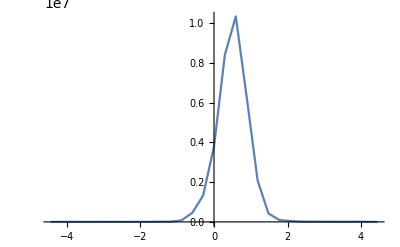

0.989974

```mathematica
(*check normalization*)
probDistr=Table[
{x,PxNa[x,.2/(80kHz)]},{x,-6l0Na,6l0Na,12l0Na/30}
];
ListPlot[probDistr,Joined->True,PlotRange->All]
Mean[Differences[probDistr[[;;,1]]]] Total[probDistr[[;;,2]]]
```

take mean of all curves at all time steps. find variance of resulting curve.

# position

## σx^2Na

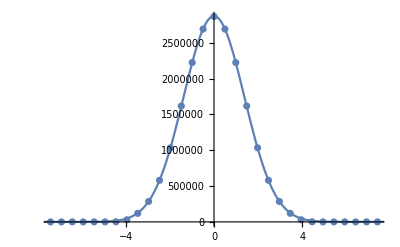

1.90728×10^-14

1.81804×10^-14

0.994543

0.990473

```mathematica
T=1/(80kHz);
nT=20;
dt=T/nT;
probDistr=Table[
{x,Sum[PxNa[x,t],{t,0,T-dt,dt}]/nT},{x,-10l0Na,10l0Na,20l0Na/30}
];


fitfn=a Exp[-(x-μ)^2/(2 σ^2)];
fit=FindFit[probDistr,fitfn,{{a,1.4 10^7},{μ,0},{σ,1 10^-8}},x];
Show[{ListPlot[probDistr,PlotRange->All],
Plot[fitfn/.fit,{x,-15l0Na,15l0Na}]
}]
varNa=σ^2/.fit
(*numerically calculate variance*)
mean=probDistr[[;;,1]].probDistr[[;;,2]];
dx=Differences[probDistr[[;;,1]]][[1]];
varNaNum=probDistr[[;;,2]].(probDistr[[;;,1]]-mean)^2 dx
(*normalized?*)

√(2π)σ a/.fit

Mean[Differences[probDistr[[;;,1]]]] Total[probDistr[[;;,2]]]
```

## σx^2Cs

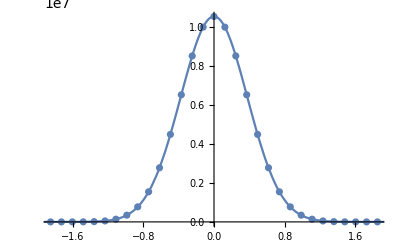

1.42548×10^-15

1.42015×10^-15

0.999777

0.999512

```mathematica
probDistr=Table[
{x,Sum[PxCs[x,t],{t,0,T-dt,dt}]/nT},{x,-6l0Cs,6l0Cs,12l0Cs/30}
];


fitfn=a Exp[-(x-μ)^2/(2 σ^2)];
fit=FindFit[probDistr,fitfn,{{a,1.4 10^7},{μ,0},{σ,1 10^-8}},x];
Show[{ListPlot[probDistr,PlotRange->All],
Plot[fitfn/.fit,{x,-15l0Cs,15l0Cs},PlotRange->All]
}]
varCs=σ^2/.fit

(*numerically calculate variance*)
mean=probDistr[[;;,1]].probDistr[[;;,2]];
dx=Differences[probDistr[[;;,1]]][[1]];
varCsNum=probDistr[[;;,2]].(probDistr[[;;,1]]-mean)^2 dx

(*normalized?*)

√(2π)σ a/.fit

Mean[Differences[probDistr[[;;,1]]]] Total[probDistr[[;;,2]]]
```

```mathematica
Sqrt[varNa+varCs]/nm
Sqrt[varNaNum+varCsNum]/nm
```

143.172

140.002

# momentum

## σx^2Na

```mathematica
T=1/(80kHz);
nT=20;
dt=T/nT;
probDistr=Table[
{p,Sum[PpNa[p,t],{t,0,T-dt,dt}]/nT},{p,-10p0Na,10p0Na,20p0Na/50}
];


fitfn=a Exp[-(p-μ)^2/(2 σ^2)];
fit=FindFit[probDistr,fitfn,{{a,1.6 10^26},{μ,0},{σ,1 10^-27}},p];
Show[{ListPlot[probDistr,PlotRange->All],
Plot[fitfn/.fit,{p,-15p0Na,15p0Na}]
}]
varNa=σ^2/.fit

(*numerically calculate variance*)
mean=0;probDistr[[;;,1]].probDistr[[;;,2]];
dx=Differences[probDistr[[;;,1]]][[1]];
varNaNum=probDistr[[;;,2]].(probDistr[[;;,1]]-mean)^2 dx

(*normalized?*)

√(2π)σ a/.fit

Mean[Differences[probDistr[[;;,1]]]] Total[probDistr[[;;,2]]]
```

-Graphics-

7.01847×10^-54

6.69016×10^-54

0.99399

0.989977

## σx^2Cs

```mathematica
probDistr=Table[
{p,Sum[PpCs[p,t],{t,0,T-dt,dt}]/nT},{p,-6p0Cs,6p0Cs,12p0Cs/30}
];


fitfn=a Exp[-(p-μ)^2/(2 σ^2)];
fit=FindFit[probDistr,fitfn,{{a,1.4 10^26},{μ,0},{σ,1 10^-27}},p];
Show[{ListPlot[probDistr,PlotRange->All],
Plot[fitfn/.fit,{p,-15p0Cs,15p0Cs},PlotRange->All]
}]
varCs=σ^2/.fit

(*numerically calculate variance*)
mean=0;probDistr[[;;,1]].probDistr[[;;,2]];
dx=Differences[probDistr[[;;,1]]][[1]];
varCsNum=probDistr[[;;,2]].(probDistr[[;;,1]]-mean)^2 dx

(*normalized?*)

√(2π)σ a/.fit

Mean[Differences[probDistr[[;;,1]]]] Total[probDistr[[;;,2]]]
```

-Graphics-

1.75423×10^-53

1.74767×10^-53

0.999777

0.999512

```mathematica
(*avg relative velocity*)
Sqrt[3]Sqrt[varNa+varCs]/((mCs mNa)/(mCs+mNa))/(nm/us)
Sqrt[3]Sqrt[varNaNum+varCsNum]/((mCs mNa)/(mCs+mNa))/(nm/us)
```

263.647

261.524

# other junk

```mathematica
SetDirectory[NotebookDirectory[]]
Export["animation.gif",list]
```

N:\Personal\lee\notebooks

animation.gif

```mathematica
l0Cs=√(ℏ/(mCs 2π 80kHz))
l0Na=√(ℏ/(mNa 2π 80kHz))
```

3.08324×10^-8

7.41164×10^-8

```mathematica
Clear[x1,x2,xCM, xrel,μ,M]


x2=xCM-m1/(m1+m2)xrel;
x1=xCM+2 m2/(m1+m2)xrel;

μ=(m1 m2)/(m1+m2);
M=m1+m2;
FullSimplify[m1 x1^2+m2 x2^2-(μ xrel^2+M xCM^2)]
```

(m1 m2 xrel (2 (m1+m2) xCM+3 m2 xrel))/(m1+m2)^2

```mathematica
xCM=(m2 x2+m1 x1)/(m1+m2);
xrel=x1-x2;

∂_xCM =m2/M D[+m1/M, x2]∂_x1;
∂_xrel =D[-∂_x2, x1];

(∂_xCM)^2=(m2/M)^2(∂_x2)^2+(m1/M)^2(∂_x1)^2+2 m2/M m1/M∂_x1 ∂_x2;
=(m2/M)^2(∂_x2)^2+(m1/M)^2(∂_x1)^2+2 μ/M∂_x1 ∂_x2;
(∂_xrel)^2 = (∂_x1)^2+(∂_x2)^2-2 ∂_x1 ∂_x2;


M (∂_xCM)^2=m2^2/M(∂_x2)^2+m1^2/M(∂_x1)^2+2 μ∂_x1 ∂_x2;
μ(∂_xrel)^2 =μ (∂_x1)^2+ μ(∂_x2)^2-2 μ ∂_x1 ∂_x2;

M (∂_xCM)^2+μ(∂_xrel)^2=(m2^2+m1m2)/M(∂_x2)^2+(m1^2+m1m2)/M(∂_x1)^2
=m2 (∂_x2)^2+m1 (∂_x1)^2
```

Γ = σ n v

n = 1/(V_pair)

V_pair = average volume occupied by pair of colliding atoms = (r.m.s. pair separation)^3

in harmonic oscillator, if trap frequencies for the 2 particles are the same, can separate into relative and CM coordinates.

problem in relative coordinates is a harmonic oscillator with reduced mass m1 m2/(m1+m2)

ground state is a gaussian with r.m.s. (ie, std dev, of sqrt(hbar/m omega))

```mathematica
ms=10^-3;
cm=10^-2;
μ=(mNa mCs)/(mNa+mCs);

n=1/(√(ℏ/(μ 2π 80kHz)))^3;
σ=1.4 10^-14 cm^2;
v=√(ℏ μ 2π 80kHz)/μ;
1/(σ n v)/ms
```

9.15693

```mathematica
v/(nm/us)
```

40.35

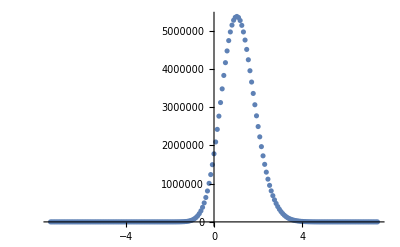

74.7998

1.87919

```mathematica
dx=l0Na/10;densityNa=Table[{x,Abs[Sum[ Pn[n,3]ψ[n,x,mNa,2π 80kHz],{n,0,20}]]^2},{x,-10 l0Na,10 l0Na,dx}];

densityNa={#[[1]],#[[2]]/(Total[densityNa[[;;,2]]]dx)}&/@densityNa;

xmean=Total[#[[1]]#[[2]]dx&/@densityNa];
stdev=√Total[(#[[1]]-xmean)^2#[[2]]dx&/@densityNa];
ListPlot[densityNa,PlotRange->All]

stdev/nm
n=1/(stdev)^3;
σ=1.4 10^-14 cm^2;
v=√((kB 70 uK)/mNa);
1/(σ n v)/ms
```

```mathematica
v/(nm/us)
```

159.075